```mathematica
keV2erg=1000 1.6022 10^-12;
is=7 2 72;
fs=2 20;
spectrumRange={{-1.3,2.3},{1,9.5}};
ionizationRange={-{75,210},{2.4,4.4}};
SetOptions[ListPlot,Frame->True,ImageSize->is,FrameStyle->Directive[Black,fs],LabelStyle->Directive[Black,fs 18/20],GridLines->Automatic,Joined->True];
green=RGBColor[{0,105,62}/255];
blue=RGBColor[{91,155,213}/255];
orange=RGBColor[{237,125,49}/255];
red=RGBColor[{192,0,0}/255];
lightGreen=RGBColor[{197,224,180}/255];
```

## Convert image to data

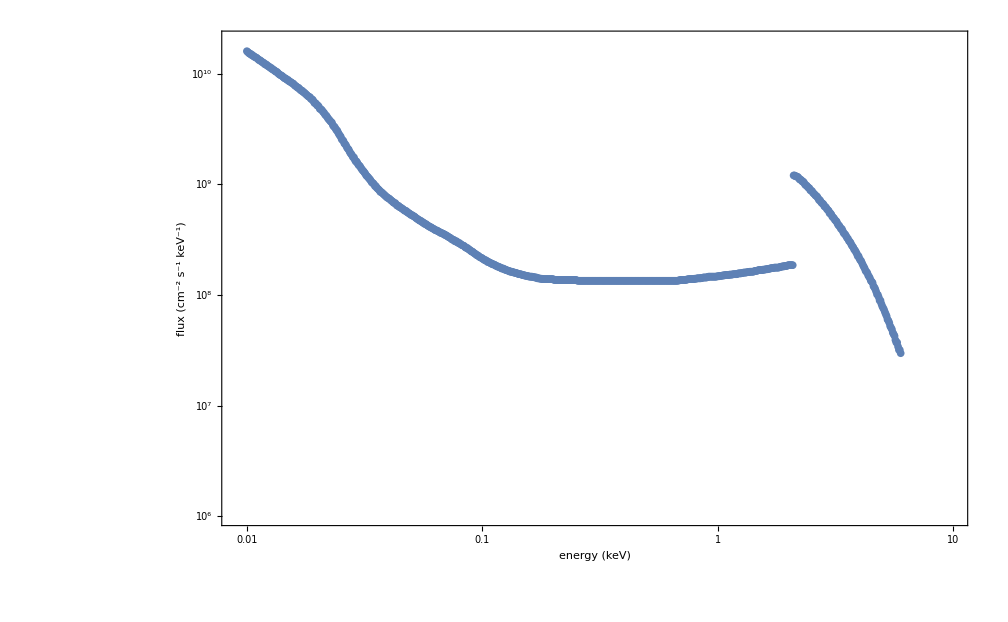

```mathematica
raw=Map[Mean,ImageData[Import["D:\\Files\\research\\thesis\\notebooks\\evans.png"]],{2}];
raw=raw/.{v_/;v<0.5->1,v_/;v>0.5->0};
vals=Replace[Length[raw]-Table[Round[Median[Flatten[Position[raw[[;;,i]],1]]]],{i,1,Dimensions[raw][[2]]}],v_/;Not[NumericQ[v]]->Missing,2];
i2E[i_]:=10^(1+(4-1)((i-1)/(Dimensions[raw][[2]]-1)))
j2F[j_]:=10^(4+(7-4)((j-1)/(Dimensions[raw][[1]]-1)))
data=Transpose[{i2E[Range[Dimensions[raw][[2]]]],j2F/@vals}]/.{_,v_}/;Not[NumericQ[v]]->Nothing//N;
ΔΩ=Integrate[Sin[θ],{θ,0,π/4},{ϕ,0,2π}](*45° solid angle*);
data=data/.{e_,f_}:>{e/1000,1000f ΔΩ};
data=Cases[data,{e_,f_}/;e≤6];
plt=ListLogLogPlot[data,Frame->True,FrameStyle->Directive[ Black,20],FrameLabel->{"energy (keV)","flux (cm^-2 s^-1 keV^-1)"},ImageSize->is,GridLines->All,PlotRange->{{0.009,10},{10^6,2 10^10}}]
```

## Fit magnetospheric part to accelerated Maxwellian of E0 = 800 eV and U0 = 2000 eV

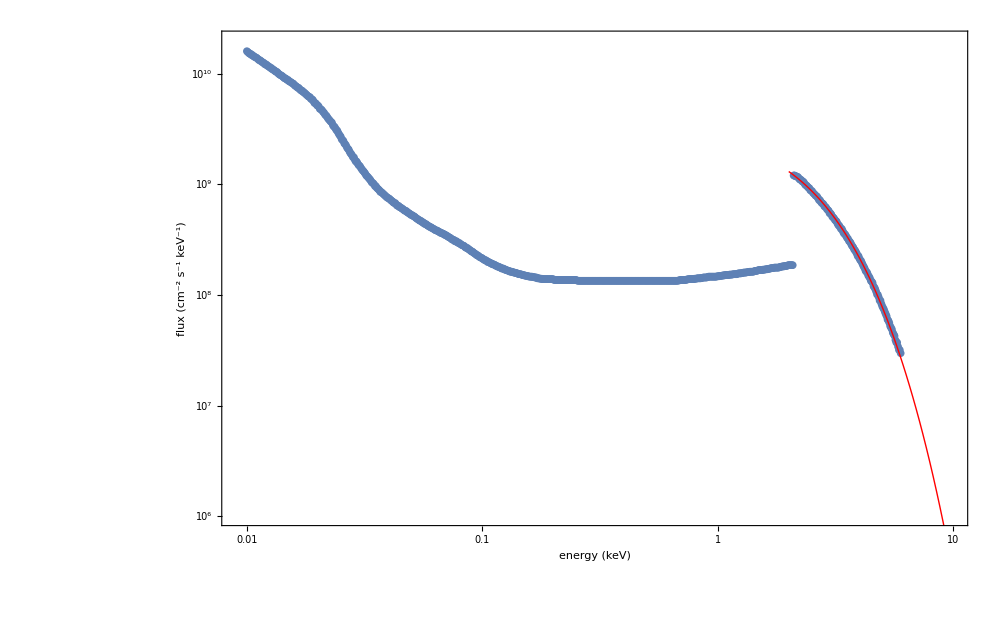

{q0→4.43802×10^9}

7.11059

```mathematica
fittingData=Cases[data,{e_,a_}/;Between[e,{2.1,6}]];
nlmf=NonlinearModelFit[fittingData,q0/(0.8^2+(0.8+2)^2)e/0.8 Exp[-(e-2)/0.8],q0,e];
Show[
plt
,LogLogPlot[nlmf[e],{e,2,10},PlotStyle->{Red,Thick}]
]
nlmf["BestFitParameters"]
Q0accFit=nlmf["BestFitParameters"][[1,2]]keV2erg
```

## Extend evans data

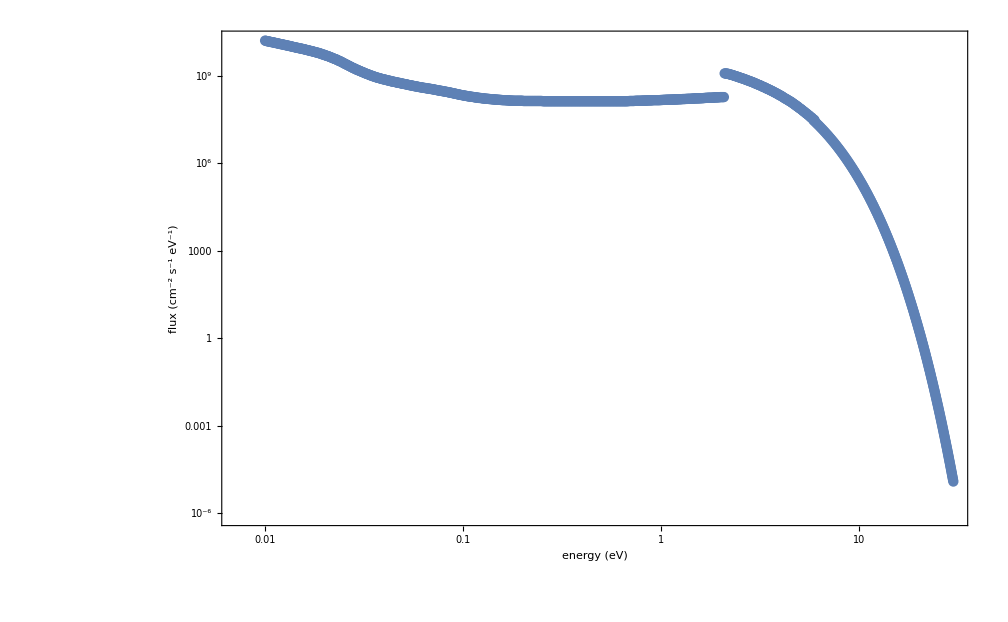

```mathematica
dataExtended=Join[data,Table[{e,nlmf[e]},{e,5.9,30,0.1}]];
ListLogLogPlot[dataExtended,Frame->True,FrameStyle->Directive[ Black,20],FrameLabel->{"energy (eV)","flux (cm^-2 s^-1 eV^-1)"},ImageSize->is,GridLines->All]
```

## GEMINIify

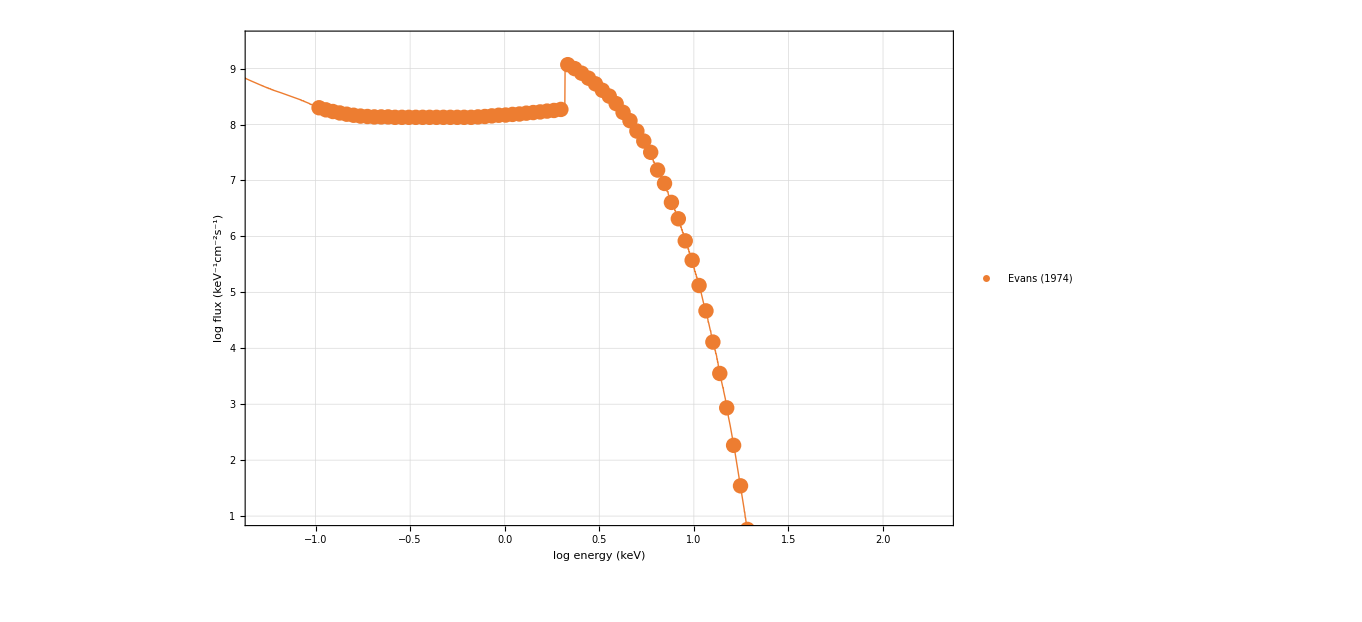

7.28384

1.99356e8_wp | 1.82982e8_wp | 1.70856e8_wp | 1.60908e8_wp
1.52842e8_wp | 1.46431e8_wp | 1.41496e8_wp | 1.39092e8_wp
1.36728e8_wp | 1.36728e8_wp | 1.36728e8_wp | 1.34404e8_wp
1.34404e8_wp | 1.34404e8_wp | 1.34404e8_wp | 1.34404e8_wp
1.34404e8_wp | 1.34404e8_wp | 1.34404e8_wp | 1.34404e8_wp
1.34404e8_wp | 1.34404e8_wp | 1.34404e8_wp | 1.36728e8_wp
1.39092e8_wp | 1.42714e8_wp | 1.46431e8_wp | 1.47692e8_wp
1.51538e8_wp | 1.54158e8_wp | 1.59534e8_wp | 1.63689e8_wp
1.67953e8_wp | 1.73810e8_wp | 1.78337e8_wp | 1.86145e8_wp
1.17517e9_wp | 0.99857e9_wp | 0.82698e9_wp | 0.67323e9_wp
0.53416e9_wp | 0.40953e9_wp | 0.32216e9_wp | 2.36630e8_wp
1.65098e8_wp | 1.17182e8_wp | 0.76341e8_wp | 0.50594e8_wp
0.31849e8_wp | 1.53359e7_wp | 0.88402e7_wp | 0.40536e7_wp
2.06401e6_wp | 0.83249e6_wp | 0.37373e6_wp | 1.32475e5_wp
0.46626e5_wp | 1.29068e4_wp | 0.35460e4_wp | 0.86002e3_wp
1.84025e2_wp | 0.34725e2_wp | 0.57766e1_wp | 0.75100e0_wp

```mathematica
phi=Interpolation[dataExtended,InterpolationOrder->0](*(keV,s^-1 cm^-2 keV^-1)*);
lbins=64;
binlb=-1;
binub=Log10[10 2];
gemE=Table[(10^(binlb+(binub-binlb)(k)/(lbins-1))+10^(binlb+(binub-binlb)(k-1)/(lbins-1)))/2,{k,1,lbins}]//N;
gemdE=Table[(10^(binlb+(binub-binlb)(k)/(lbins-1))-10^(binlb+(binub-binlb)(k-1)/(lbins-1))),{k,1,lbins}]//N;
gemPhi=phi/@gemE;
pltEvans=Show[
ListPlot[
Transpose[{Log10[gemE],Log10[gemPhi]}]
,FrameLabel->{"log energy (keV)","log flux (keV^-1cm^-2s^-1)"}
,PlotStyle->orange
,PlotRange->spectrumRange
,PlotLegends->Placed[PointLegend[{"Evans (1974)"},LegendMarkerSize->20],{Left,Bottom}]
,Joined->False
]
,Plot[Log10[phi[10^e]],{e,-2,3},PlotStyle->{Thick,orange(*,Dashing[{0.01,0.005}]*)}]
]
Q0=Total[gemE gemPhi gemdE]keV2erg
Partition[With[{p=Round[Log10[#]]},ToString[SetAccuracy[#/10^p,6]]<>"e"<>ToString[p]<>"_wp"]&/@gemPhi,4]//TableForm
```

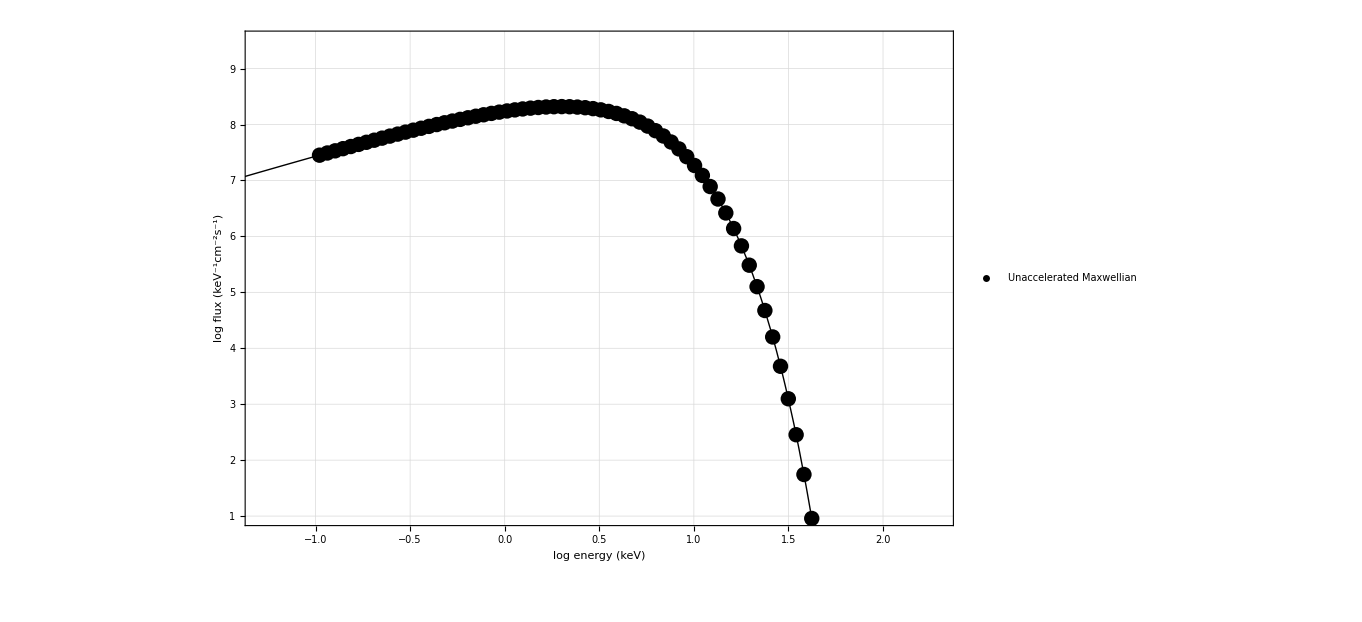

7.27821

```mathematica
binlb=-1;
binub=Log10[20 2];
gemE=Table[(10^(binlb+(binub-binlb)(k)/(lbins-1))+10^(binlb+(binub-binlb)(k-1)/(lbins-1)))/2,{k,1,lbins}]//N;
gemdE=Table[(10^(binlb+(binub-binlb)(k)/(lbins-1))-10^(binlb+(binub-binlb)(k-1)/(lbins-1))),{k,1,lbins}]//N;
gemPhi=(Q0/keV2erg)/(2 2^3)gemE Exp[-gemE/2];
pltMax=Show[
ListPlot[
Transpose[{Log10[gemE],Log10[gemPhi]}]
,FrameLabel->{"log energy (keV)","log flux (keV^-1cm^-2s^-1)"}
,PlotStyle->Black
,PlotRange->spectrumRange
,PlotLegends->Placed[PointLegend[{"Unaccelerated Maxwellian"},LegendMarkerSize->20],{Left,Bottom}]
,Joined->False
]
,Plot[Log10[(Q0/keV2erg)/(2 2^3)10^e Exp[-10^e/2]],{e,-3,3},PlotStyle->{Thick,Black}]
]
Total[gemE gemPhi gemdE]keV2erg
```

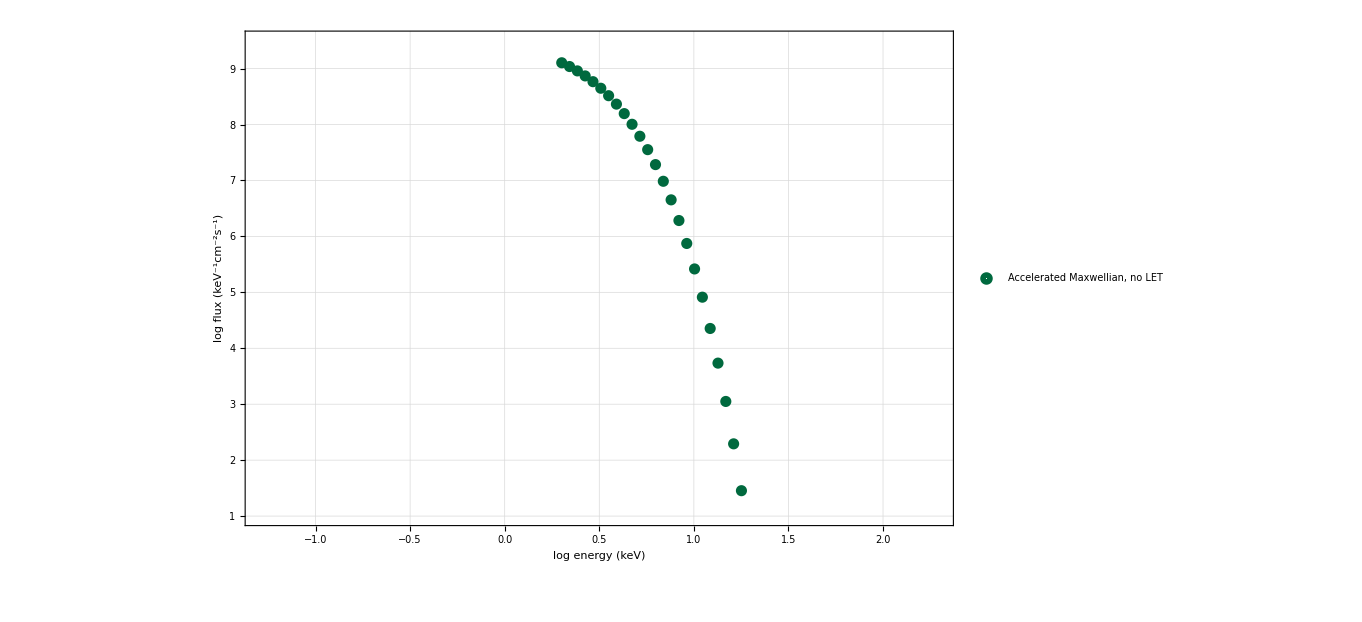

7.28243

```mathematica
binlb=-1;
binub=Log10[20 2];
gemE=Table[(10^(binlb+(binub-binlb)(k)/(lbins-1))+10^(binlb+(binub-binlb)(k-1)/(lbins-1)))/2,{k,1,lbins}]//N;
gemdE=Table[(10^(binlb+(binub-binlb)(k)/(lbins-1))-10^(binlb+(binub-binlb)(k-1)/(lbins-1))),{k,1,lbins}]//N;
gemPhi=(0.949Q0/keV2erg)/(0.8^2+(0.8+2)^2)(gemE/.v_/;v<2->0)/0.8 Exp[-(gemE-2)/0.8];
pltEvansNoLET=Show[
ListPlot[
Transpose[{Log10[gemE],Log10[gemPhi]}]
,FrameLabel->{"log energy (keV)","log flux (keV^-1cm^-2s^-1)"}
(*,PlotMarkers->"OpenMarkers"*)
,PlotMarkers->{Graphics[{Thickness[0.2],Circle[{0,0},0.1]}],Scaled[0.04]}
,PlotStyle->{green,PointSize[0.015]}
,PlotRange->spectrumRange
,PlotLegends->Placed[PointLegend[{"Accelerated Maxwellian, no LET"},LegendMarkerSize->20],{Left,Bottom}]
,Joined->False
]
,Plot[Log10[(Q0accFit/keV2erg)/(0.8^2+(0.8+2)^2)10^e/0.8 Exp[-(10^e-2)/0.8]],{e,Log10[2],200},PlotStyle->{Thickness[0.005],green,Opacity[0]}]
]
Total[gemE gemPhi gemdE]keV2erg
```

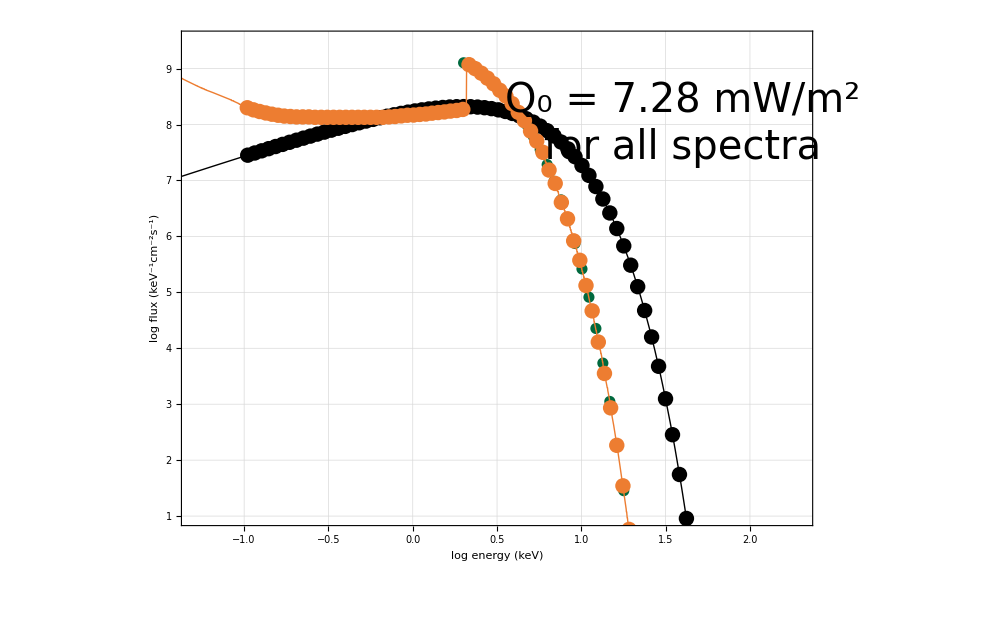

D:\Files\research\CEDAR 2023\figures\evans_comp.png

```mathematica
plt=Show[pltMax,pltEvansNoLET,pltEvans,Epilog->{Text[Style["Q_0 = 7.28 mW/m^2
for all spectra",fs],{1.6,8}]}]
Export["D:\\Files\\research\\CEDAR 2023\\figures\\evans_comp.png",plt]
```

```mathematica
7.28384/keV2erg
```

4.54615×10^9

## GEMINI Output

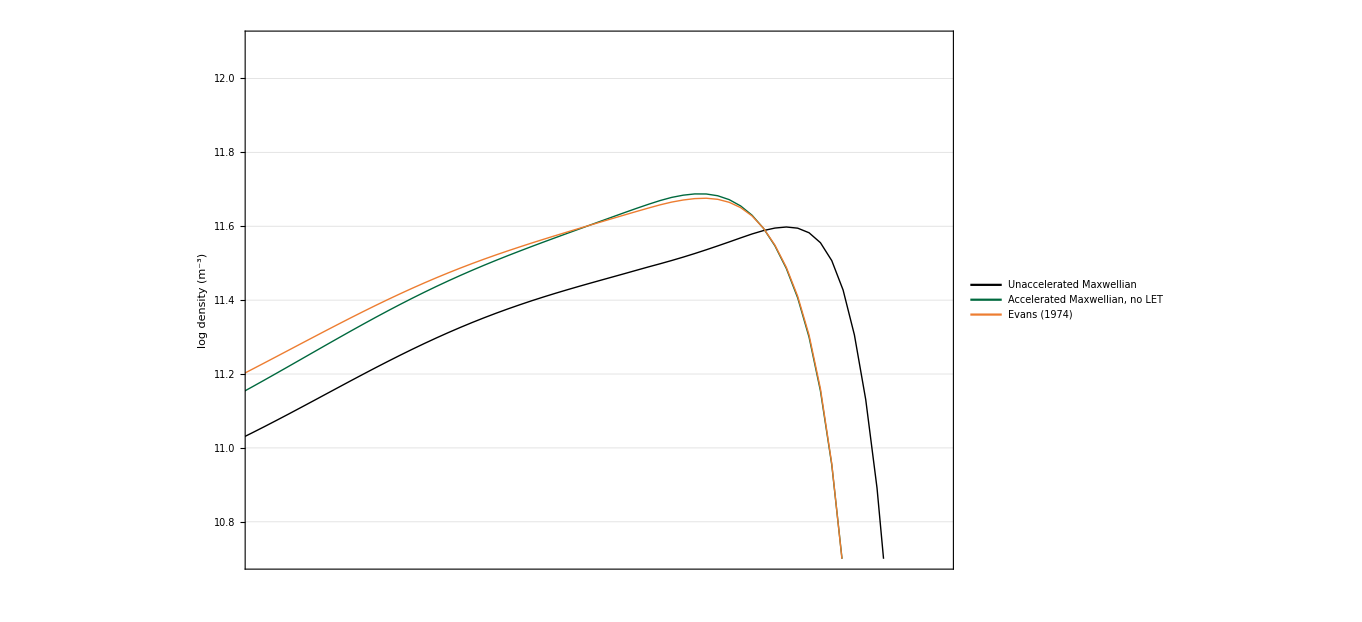

```mathematica
alt=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_01\\inputs\\simgrid.h5","/x1"][[3;;-3]]/1000;
neEvans=Log10[Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_01\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]]];
neMax=Log10[Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_02\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]]];
neEvansNoLET=Log10[Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_03\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]]];
pltA=ListPlot[{
Transpose[{-alt,neMax}]
,Transpose[{-alt,neEvansNoLET}]
,Transpose[{-alt,neEvans}]
}
,FrameLabel->{None,"log density (m^-3)"}
,FrameTicks->{{Automatic,None},{None,None}}
,PlotRange->{-{85,210},{10.7,12.1}}
,PlotLegends->Placed[{"Unaccelerated Maxwellian","Accelerated Maxwellian, no LET","Evans (1974)"},{Left,Top}]
,PlotStyle->({#,Thick,Dashing[None]}&/@{Black,green,orange})
]
```

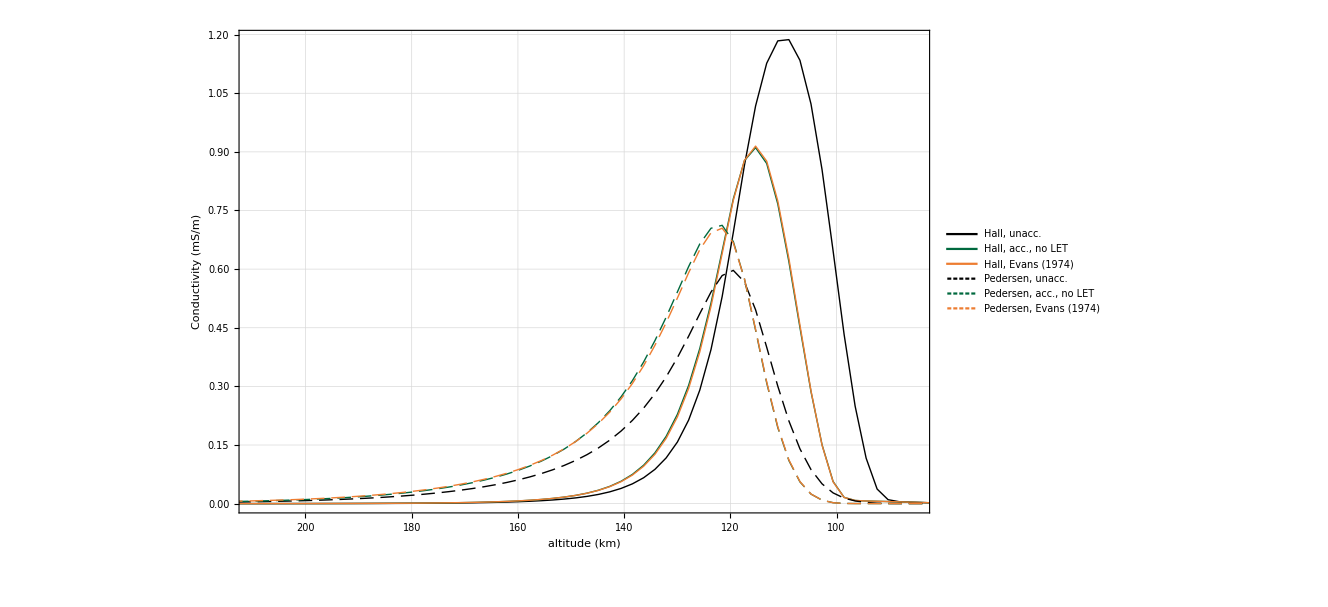

```mathematica
sigEvans=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_01\\conductances\\20150201T100000.000UT_sig.mat"]1000;
sigMax=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_02\\conductances\\20150201T100000.000UT_sig.mat"]1000;
sigEvansNoLET=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_03\\conductances\\20150201T100000.000UT_sig.mat"]1000;
sigPEvans=sigEvans[[1,216/2,;;,1]];
sigHEvans=-sigEvans[[2,216/2,;;,1]];
sigPMax=sigMax[[1,216/2,;;,1]];
sigHMax=-sigMax[[2,216/2,;;,1]];
sigPEvansNoLET=sigEvansNoLET[[1,216/2,;;,1]];
sigHEvansNoLET=-sigEvansNoLET[[2,216/2,;;,1]];
pltB=ListPlot[{
Transpose[{-alt,sigHMax}]
,Transpose[{-alt,sigHEvansNoLET}]
,Transpose[{-alt,sigHEvans}]
,Transpose[{-alt,sigPMax}]
,Transpose[{-alt,sigPEvansNoLET}]
,Transpose[{-alt,sigPEvans}]
}
,FrameLabel->{"altitude (km)","Conductivity (mS/m)"}
,FrameTicks->{{Automatic,None},{Table[{a,-a},{a,-200,-80,20}],None}}
,PlotRange->{-{85,210},All}
,PlotLegends->Placed[{"Hall, unacc.","Hall, acc., no LET","Hall, Evans (1974)","Pedersen, unacc.","Pedersen, acc., no LET","Pedersen, Evans (1974)"},{Left,Top}]
,ImageSize->0.976is
,PlotStyle->Flatten[Table[{c,Thick,Dashing[d]},{d,{None,{0.01,0.005}}},{c,{Black,green,orange}}],1]
]
```

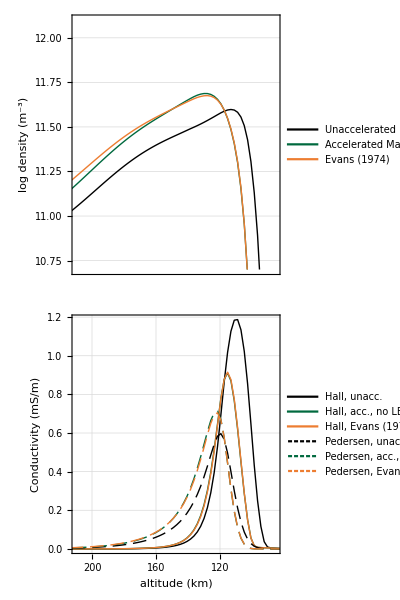

D:\Files\research\CEDAR 2023\figures\conductivities.png

```mathematica
plt=Column[{pltA,pltB},Spacings->-0.3,Alignment->Right]
Export["D:\\Files\\research\\CEDAR 2023\\figures\\conductivities.png",plt]
```

```mathematica
lb1=1;
ub1=100;
lb3=70;
ub3=180;
x1=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_04\\inputs\\simgrid.h5","/x1"][[3;;-3]][[lb1;;ub1]]/1000;x2=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_04\\inputs\\simgrid.h5","/x2"][[3;;-3]]/1000;
x3=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_04\\inputs\\simgrid.h5","/x3"][[3;;-3]][[lb3;;ub3]]/1000;
j1Unacc=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_04\\20150201_36000.000000.h5","/J1all"][[lb3;;ub3,1,lb1;;ub1]] 10^6;
j2Unacc=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_04\\20150201_36000.000000.h5","/J2all"][[lb3;;ub3,1,lb1;;ub1]] 10^6;
j3Unacc=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_04\\20150201_36000.000000.h5","/J3all"][[lb3;;ub3,1,lb1;;ub1]] 10^6;j1Acc=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_05\\20150201_36000.000000.h5","/J1all"][[lb3;;ub3,1,lb1;;ub1]] 10^6;
j2Acc=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_05\\20150201_36000.000000.h5","/J2all"][[lb3;;ub3,1,lb1;;ub1]] 10^6;
j3Acc=Import["D:\\Files\\research\\thesis\\runs\\evans_comparison_05\\20150201_36000.000000.h5","/J3all"][[lb3;;ub3,1,lb1;;ub1]] 10^6;
```

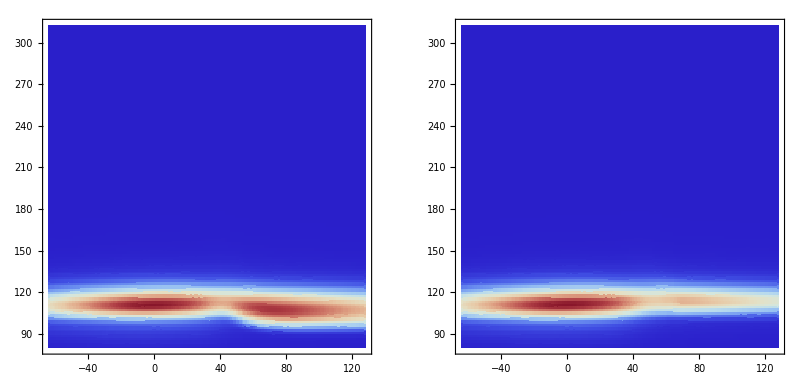

```mathematica
vecsUnacc=Flatten[Table[{{x3[[i3]],x1[[i1]]},{j3Unacc[[i3,i1]],j1Unacc[[i3,i1]]}},{i1,1,Length[x1]},{i3,1,Length[x3]}],1];
vecsAcc=Flatten[Table[{{x3[[i3]],x1[[i1]]},{j3Acc[[i3,i1]],j1Acc[[i3,i1]]}},{i1,1,Length[x1]},{i3,1,Length[x3]}],1];
densUnacc=Flatten[Table[{x3[[i3]],x1[[i1]],j2Unacc[[i3,i1]]},{i1,1,Length[x1]},{i3,1,Length[x3]}],1];
densAcc=Flatten[Table[{x3[[i3]],x1[[i1]],j2Acc[[i3,i1]]},{i1,1,Length[x1]},{i3,1,Length[x3]}],1];
pltA=ListStreamPlot[vecsUnacc,StreamStyle->Blue,ImageSize->1000,StreamScale->None];
pltAdens=ListDensityPlot[densUnacc,InterpolationOrder->0,ColorFunction->"ThermometerColors",PlotRange->{0,30}];
pltB=ListStreamPlot[vecsAcc,StreamStyle->Red,ImageSize->1000,StreamScale->None];
pltBdens=ListDensityPlot[densAcc,InterpolationOrder->0,ColorFunction->"ThermometerColors",PlotRange->{0,30}];
GraphicsRow[{Show[pltA,pltAdens],Show[pltB,pltBdens]},ImageSize->Full]
```

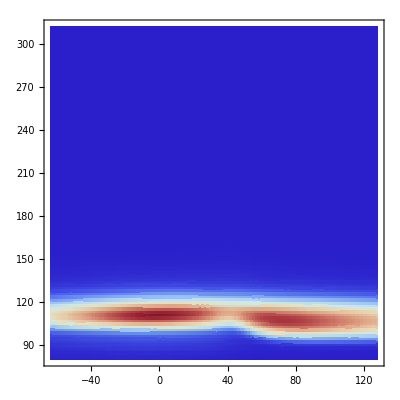

```mathematica
pltAdens
```

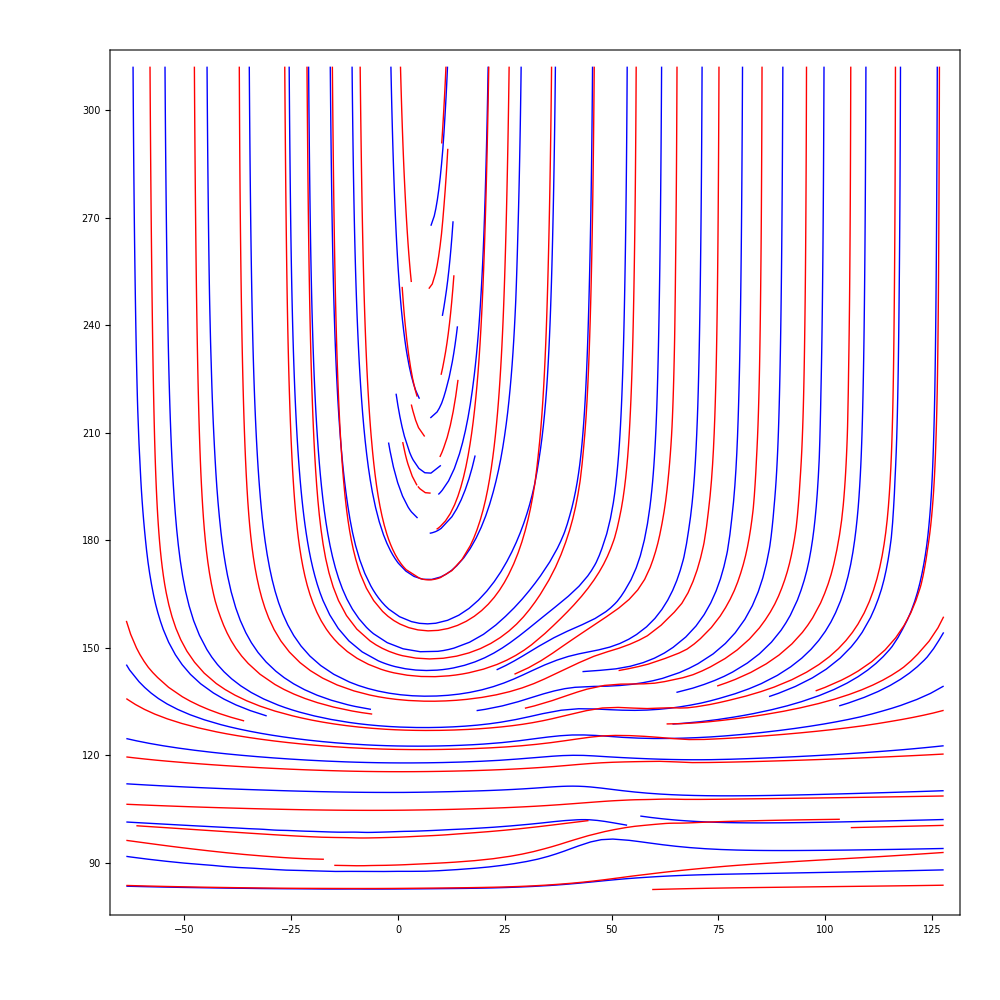

```mathematica
Show[pltA,pltB]
```